## Classical Dynamics

## Verlet Algorithm

```mathematica
V[x_]=k x^2/2;
F[x_]=-k x;
```

```mathematica
Subs={k->1,m->1};
```

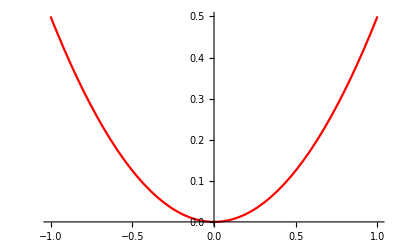

```mathematica
VPlot=Plot[V[x]/.Subs,{x,-1,1},PlotStyle->Red]
```

```mathematica
Time=10;
dt=0.1;
nSteps=Round[Time/dt]
```

100

```mathematica
x0=-0.8;
v0=0;
```

```mathematica
x[0]=x0;
x[1]=x0;
(*f[1]=F[x[1]]/.Subs;*)
Do[x[n+1]=2 x[n]+dt^2 F[x[n]]/m-x[n-1]/.Subs,{n,1,nSteps}]
```

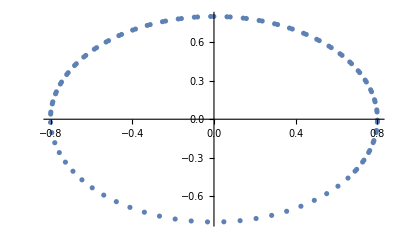

```mathematica
xData=Table[{n dt,x[n]},{n,0,nSteps}];
xPlot=ListPlot[xData];
vData=Table[{n dt,(x[n+1]-x[n-1])/(2dt)},{n,1,nSteps}];
vPlot=ListPlot[vData];
xvData=Table[{x[n],(x[n+1]-x[n-1])/(2dt)},{n,1,nSteps}];
xvPlot=ListPlot[xvData]
```

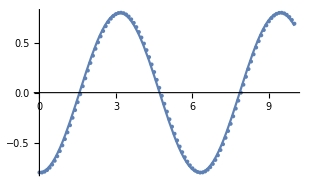

```mathematica
anaxPlot=Plot[x0 Cos[Sqrt[k/m]t]/.Subs,{t,0,Time}];
Show[anaxPlot,xPlot]
```

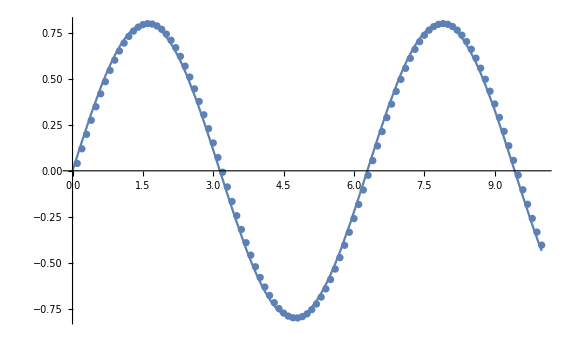

```mathematica
anavPlot=Plot[-x0 Sqrt[k/m]Sin[Sqrt[k/m]t]/.Subs,{t,0,Time}];
Show[anavPlot,vPlot]
```

## Velocity Verlet Algorithm

```mathematica
V[x_]=k x^2/2;
F[x_]=-k x;
```

```mathematica
Subs={k->1,m->1};
```

```mathematica
VPlot=Plot[V[x]/.Subs,{x,-1,1},PlotStyle->Red]
```

-Graphics-

```mathematica
Time=10;
dt=0.1;
nSteps=Round[Time/dt]
```

100

```mathematica
x0=-0.8;
v0=0;
```

```mathematica
x[0]=x0;
v[0]=v0;
f[0]=F[x[0]]/.Subs;
Do[{
x[n+1]= x[n]+v[n]dt+dt^2f[n]/(2 m)/.Subs;
f[n+1]=F[x[n+1]];
v[n+1]=v[n]+(dt/m)(1/2)(f[n]+f[n+1])/.Subs;
},{n,0,nSteps}]
```

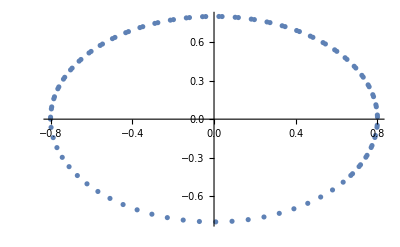

```mathematica
xData=Table[{n dt,x[n]},{n,0,nSteps}];
xPlot=ListPlot[xData];
vData=Table[{n dt,v[n]},{n,0,nSteps}];
vPlot=ListPlot[vData];
xvData=Table[{x[n],v[n]},{n,0,nSteps}];
xvPlot=ListPlot[xvData]
```

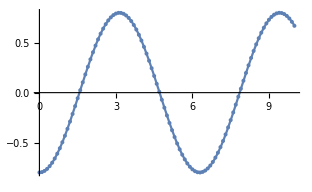

```mathematica
anaxPlot=Plot[x0 Cos[Sqrt[k/m]t]/.Subs,{t,0,Time}];
Show[anaxPlot,xPlot]
```

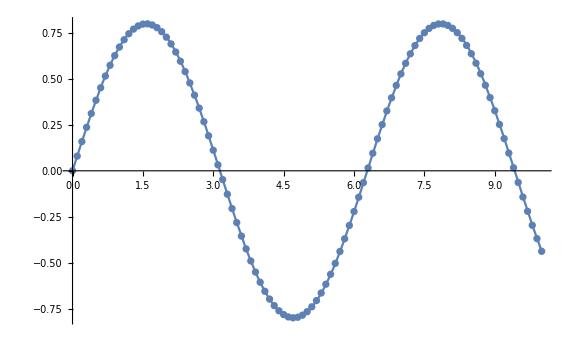

```mathematica
anavPlot=Plot[-x0 Sqrt[k/m]Sin[Sqrt[k/m]t]/.Subs,{t,0,Time}];
Show[anavPlot,vPlot]
```

## Colinear Reaction

```mathematica
Vlj[r_]=4ϵ((σ/r)^12-(σ/r)^6);
Flj[r_]=24ϵ(2σ^12/r^13-σ^6/r^7);
```

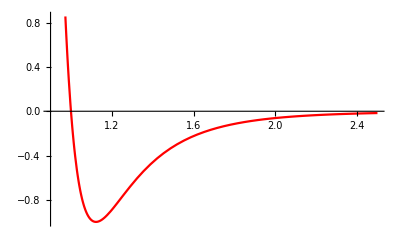

```mathematica
rMin=0.9;rMax=2.5;
Plot[Vlj[r]/.Subs,{r,rMin,rMax},PlotStyle->Red]
```

```mathematica
FindMinimum[Vlj[r]/.Subs,r]
```

{-1.,{r→1.12246}}

```mathematica
V[rAB_,rBC_]=Vlj[rAB]+Vlj[rBC]+Vlj[rAB+rBC]
```

4 ϵ (-σ^6/rAB^6+σ^12/rAB^12)+4 ϵ (-σ^6/rBC^6+σ^12/rBC^12)+4 ϵ (-σ^6/(rAB+rBC)^6+σ^12/(rAB+rBC)^12)

```mathematica
Subs={ϵ->1,σ->1,m->1};
```

```mathematica
VPlot=Plot3D[V[rAB,rBC]/.Subs,{rAB,rMin,rMax},{rBC,rMin,rMax}]
```

-Graphics3D-

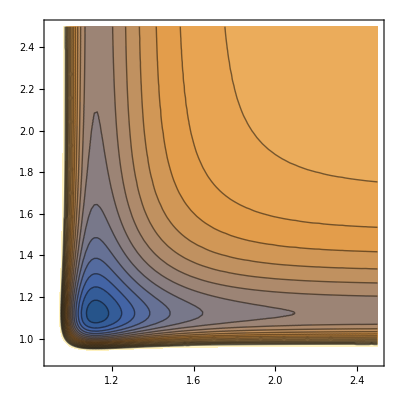

```mathematica
VPlot=ContourPlot[V[rAB,rBC]/.Subs,{rAB,rMin,rMax},{rBC,rMin,rMax},Contours->20]
```

```mathematica
Time=100;
dt=0.01;
nSteps=Round[Time/dt]
```

10000

```mathematica
xA0=-2.5;
xB0=0;
xC0=1.1;
vA0=0.1;
vB0=0;
vC0=0;
```

```mathematica
xA[0]=xA0;
xB[0]=xB0;
xC[0]=xC0;
vA[0]=vA0;
vB[0]=vB0;
vC[0]=vC0;
fA[0]=-Flj[xB[0]-xA[0]]-Flj[xC[0]-xA[0]]/.Subs;
fB[0]=+Flj[xB[0]-xA[0]]-Flj[xC[0]-xB[0]]/.Subs;
fC[0]=+Flj[xC[0]-xA[0]]+Flj[xC[0]-xB[0]]/.Subs;
Do[{
xA[n+1]= xA[n]+vA[n]dt+dt^2fA[n]/(2 m)/.Subs;
xB[n+1]= xB[n]+vB[n]dt+dt^2fB[n]/(2 m)/.Subs;
xC[n+1]= xC[n]+vC[n]dt+dt^2fC[n]/(2 m)/.Subs;
fA[n+1]=-Flj[xB[n+1]-xA[n+1]]-Flj[xC[n+1]-xA[n+1]]/.Subs;
fB[n+1]=+Flj[xB[n+1]-xA[n+1]]-Flj[xC[n+1]-xB[n+1]]/.Subs;
fC[n+1]=+Flj[xC[n+1]-xA[n+1]]+Flj[xC[n+1]-xB[n+1]]/.Subs;
vA[n+1]=vA[n]+(dt/m)(1/2)(fA[n]+fA[n+1])/.Subs;
vB[n+1]=vB[n]+(dt/m)(1/2)(fB[n]+fB[n+1])/.Subs;
vC[n+1]=vC[n]+(dt/m)(1/2)(fC[n]+fC[n+1])/.Subs;
},{n,0,nSteps}]
```

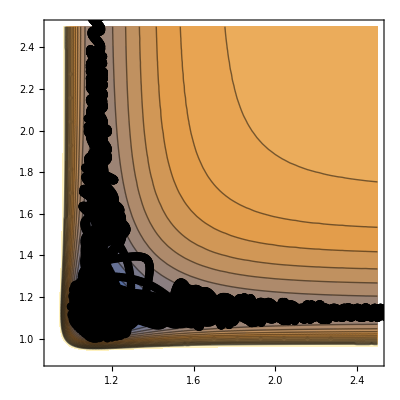

```mathematica
rData=Table[{xB[n]-xA[n],xC[n]-xB[n]},{n,0,nSteps}];
rPlot=ListPlot[rData,Mesh->All,Joined->True,PlotStyle->Black];
Show[VPlot,rPlot]
```

```mathematica
Animate[ListPlot[{{xA[n],0},{xB[n],0},{xC[n],0}},PlotStyle->PointSize[0.1],PlotRange->{{-3,3},{-1,1}}],{n,0,nSteps,1}]
```

## More Dimensions

```mathematica
Subs={ϵ->1,σ->1,m->1};
```

```mathematica
Vlj1D[r_]:=4ϵ((σ/r)^12-(σ/r)^6)
Flj1D[r_]:=24ϵ(2σ^12/r^13-σ^6/r^7)
```

```mathematica
Vlj3D[rij_]:=Module[{rijmag=Sqrt[rij.rij]},
Vlj1D[rijmag]]
Flj3D[rij_]:=Module[{rijmag=Sqrt[rij.rij]},
-Flj1D[rijmag]rij/rijmag]
```

```mathematica
Vlj[r_]:=Module[{nAtoms=Length[r],Vtot=0},
For[i=1,i≤nAtoms,i++,
For[j=i+1,j≤nAtoms,j++,
rij=r[[j]]-r[[i]];
Vtot=Vtot+Vlj3D[rij];
];
];
Vtot
]
Flj[r_]:=Module[{nAtoms=Length[r],Ftot=0*r},
For[i=1,i≤nAtoms,i++,
For[j=i+1,j≤nAtoms,j++,
rij=r[[j]]-r[[i]];
Ftot[[i]]=Ftot[[i]]+Flj3D[rij];
Ftot[[j]]=Ftot[[j]]-Flj3D[rij];
];
];
Ftot
]
```

```mathematica
rtest={{0,0,0},{1.1,0,0}}
Flj[rtest]/.Subs
```

{{0,0,0},{1.1,0,0}}

{{-1.5881,0.,0.},{1.5881,0.,0.}}

```mathematica
Time=20;
dt=0.01;
nSteps=Round[Time/dt]
```

2000

```mathematica
x={{-5,0,0},{-1,0,0},{1,0,0},{1,1,0},{0,0,1},{1,1,1}};
v={{5,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}};
```

```mathematica
xData={x};
f=Flj[x]/.Subs;
Do[{
x= x+v dt+dt^2f(2 m)/.Subs;
fold=f;
f=Flj[x]/.Subs;
v=v+(dt/m)(1/2)(fold+f)/.Subs;
xData=Append[xData,x];
},{n,0,nSteps}]
```

## 3 D Visualizer

```mathematica
box=5;
trajdata=xData;
Nsteps=Length[trajdata];
Natoms=Length[trajdata[[1]]];Animate[Graphics3D[{Blue,GraphicsComplex[trajdata[[n]],Table[Sphere[i,0.5],{i,Natoms}]]},PlotRange->{{-box,box},{-box,box},{-box,box}},BoxRatios->{1,1,1},Axes->False],{n,1,Nsteps,1}]
```